```mathematica
Integrate[Exp[-β px^2/2/m],{px,-Infinity,Infinity}]//FullSimplify
```

ConditionalExpression[(√(2 π))/(√(β/m)),Re[β/m]>0]

```mathematica
D[Log[(2π m k T/h^2)^(3/2)(k T(L-2ra)^2/(q E0)(Exp[-q E0 ra/k/T]-Exp[-q E0 (L-ra)/k/T])+k T(L-2rc)^2/(q E0)(Exp[q E0 (L-rc)/k/T]-Exp[q E0 rc/k/T]))],L]//FullSimplify
```

(2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T))/(k ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2) T)

```mathematica
N1 k T/3/L^2((2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T))/(k ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2) T))
```

(N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2))

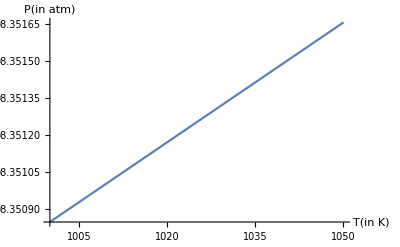

```mathematica
Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=15*10^3},
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,1000,1050},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

```mathematica
Manipulate[Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0},
ContourPlot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))==λ atm,{T,1000,1500},{E0,1,1500},AxesLabel->{"T(in K)","E0(in V/m)"}]
],{λ,1,10}]
```

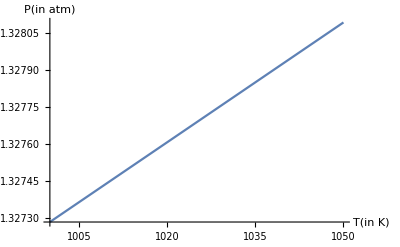

```mathematica
Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=200},
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,1000,1050},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

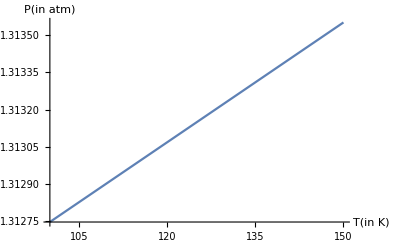

```mathematica
Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=200},
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,100,150},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

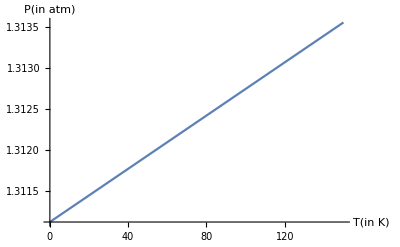

```mathematica
Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=200},
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,0,150},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

```mathematica
Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=200},
Print["One limit of the electric field =",k (1000)/(q L)];
Print["Another limit of the electric field =",9*10^9*q^2/(ra^2)];
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,0,150},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

One limit of the electric field =1.23214

Another limit of the electric field =1.02811×10^-8

-Graphics-

```mathematica
Manipulate[Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^19,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0},
ContourPlot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))==λ atm*10^18,{T,1000,1500},{E0,10^8,10^9},AxesLabel->{"T(in K)","E0(in V/m)"}]
],{λ,1,10}]
```

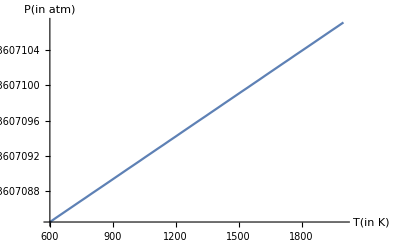

```mathematica
Block[(*Sodium chloride, Na+ = 149.7 pm, Cl- = 218.1 pm*)
{atm=10^5,N1=6.023*10^13,k=1.38*10^(-23),T,ra=149.7*10^(-12),rc=218.1*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=5.68*10^8},
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,600,2000},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

```mathematica
D[-2q E0 V^(1/3)(1+V^(1/3)/a),V]//FullSimplify
```

-(2 E0 q (a+2 V^(1/3)))/(3 a V^(2/3))

```mathematica
D[(V k T/(2a^3)Log[V/2/a^3]+q E0 V/a^2),V]
```

(E0 q)/a^2+(k T)/(2 a^3)+(k T Log[V/(2 a^3)])/(2 a^3)

```mathematica
N[2/Sqrt[3](174+181)]
```

409.919

```mathematica
2*10^4*(409.919*10^(-12))^2/(1.6*10^(-19))
```

21004.2

32.0919

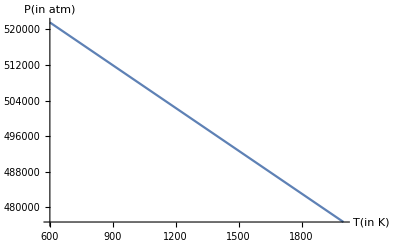

```mathematica
Block[(*Caesium chloride, Cs+ = 174 pm, Cl- = 181 pm*)
{atm=10^5,N1=6.023*10^13,k=1.38*10^(-23),T,ra=174*10^(-12),rc=181*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=5.68*10^10,V,a},
a=2/Sqrt[3](ra+rc);
V=N1 a^3;
Print[(k/(2 a^3)+(k Log[V/(2 a^3)])/(2 a^3))/atm];
Plot[((E0 q)/a^2-(k T)/(2 a^3)-(k T Log[V/(2 a^3)])/(2 a^3))/atm,{T,600,2000},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

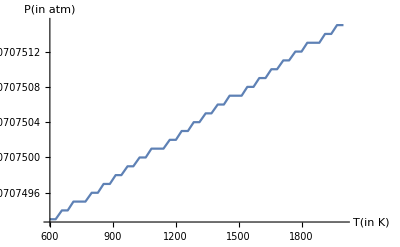

```mathematica
Block[(*Caesium chloride, Cs+ = 174 pm, Cl- = 181 pm*)
{atm=10^5,N1=6.023*10^13,k=1.38*10^(-23),T,ra=174*10^(-12),rc=181*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=5.68*10^10},
Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,600,2000},AxesLabel->{"T(in K)","P(in atm)"}]
]
```

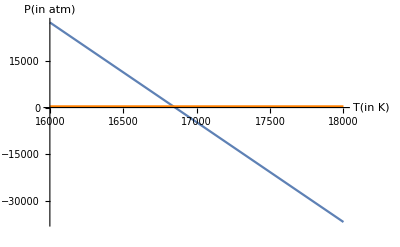

```mathematica
Block[(*Caesium chloride, Cs+ = 174 pm, Cl- = 181 pm*)
{atm=10^5,N1=6.023*10^13,k=1.38*10^(-23),T,ra=174*10^(-12),rc=181*10^(-12),q=1.6*10^(-19),L=7*10^(-2),E0=5.68*10^10,V,a},
a=2/Sqrt[3](ra+rc);
V=N1 a^3;
Show[
Plot[((E0 q)/a^2-(k T)/(2 a^3)-(k T Log[V/(2 a^3)])/(2 a^3))/atm,{T,1.6*10^4,1.8*10^4},AxesLabel->{"T(in K)","P(in atm)"}],Plot[((N1 (2 ⅇ^(-(E0 q ra)/(k T)) k (L-2 ra) T+2 ⅇ^((E0 q rc)/(k T)) k (-L+2 rc) T+ⅇ^((E0 q (-L+ra))/(k T)) (L-2 ra) (E0 q (L-2 ra)-2 k T)+ⅇ^((E0 q (L-rc))/(k T)) (L-2 rc) (E0 q (L-2 rc)+2 k T)))/(3 L^2 ((ⅇ^(-(E0 q ra)/(k T))-ⅇ^((E0 q (-L+ra))/(k T))) (L-2 ra)^2+(ⅇ^((E0 q (L-rc))/(k T))-ⅇ^((E0 q rc)/(k T))) (L-2 rc)^2)))/atm,{T,1.6*10^4,1.8*10^4},AxesLabel->{"T(in K)","P(in atm)"},PlotStyle->Orange],PlotStyle->Automatic
]
]
```